# Pango analysis: Plotting partitioned case counts and Rt

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Documents/src/rt-from-frequency-dynamics/results/pango-countries

## Setup

### Parameters

```mathematica
dataset="pango-countries";
```

```mathematica
model="GARW";
```

```mathematica
imageSize=300;
```

```mathematica
gridCount=1;
```

```mathematica
rtMax=2.0;
```

```mathematica
rtMin=0.6;
```

### Date ticks

```mathematica
dateTicks={"2021-10-01","2021-11-01","2021-12-01","2022-01-01","2022-02-01","2022-03-01","2022-04-01","2022-05-01","2022-06-01","2022-07-01","2022-08-01","2022-09-01","2022-10-01","2022-11-01","2022-12-01"};
```

### Countries

```mathematica
countriesToDrop={};
```

## Variants and colors

### Import

```mathematica
variantData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_Rt-combined-"<>model<>".tsv"];
```

```mathematica
header=variantData[[1]]
```

{date,location,variant,median_R,R_upper_95,R_lower_95,R_upper_80,R_lower_80,R_upper_50,R_lower_50,median_freq}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_R→4,R_upper_95→5,R_lower_95→6,R_upper_80→7,R_lower_80→8,R_upper_50→9,R_lower_50→10,median_freq→11}

```mathematica
variantData=Drop[variantData,1];
```

```mathematica
variants=Union[variantData[[All,3]]]
```

{BA.2.3.20,BA.2.75,BA.2.75.2,BA.4.6,BA.5,BA.5.1,BA.5.1.10,BA.5.1.12,BA.5.1.18,BA.5.1.27,BA.5.1.30,BA.5.1.5,BA.5.1.6,BA.5.2,BA.5.2.1,BA.5.2.16,BA.5.2.20,BA.5.2.21,BA.5.2.23,BA.5.2.34,BA.5.2.35,BA.5.2.6,BA.5.2.9,BA.5.5,BA.5.5.1,BA.5.6,BE.1,BE.1.1,BE.1.1.1,BE.1.2.1,BE.1.4.2,BE.4,BF.10,BF.11,BF.13,BF.14,BF.26,BF.5,BF.7,BF.7.4,BF.7.4.1,BF.7.5,BN.1,BN.1.2,BN.1.3,BN.1.3.1,BN.1.4,BN.1.5,BQ.1,BQ.1.1,BQ.1.10,BQ.1.10.1,BQ.1.11,BQ.1.1.18,BQ.1.12,BQ.1.1.3,BQ.1.13,BQ.1.1.4,BQ.1.14,BQ.1.1.5,BQ.1.15,BQ.1.1.7,BQ.1.2,BQ.1.22,BQ.1.23,BQ.1.25,BQ.1.3,BQ.1.5,BQ.1.6,BQ.1.8,BW.1,CH.1.1,CK.1,CQ.2,CR.1.1,other,XBB,XBB.1,XBB.1.5,XBB.2}

```mathematica
n=Length[variants]
```

80

### Max frequency

```mathematica
variantFrequencyMapping=Table[variant->Max[Cases[variantData,x_/;x[[3]]==variant][[All,11]]],{variant,variants}];
```

```mathematica
highFrequencyVariants=Cases[variantFrequencyMapping,x_/;x[[2]]>=0.005][[All,1]];
```

```mathematica
Length[highFrequencyVariants]
```

58

```mathematica
lowFrequencyVariants=Complement[variants,highFrequencyVariants];
```

```mathematica
Length[lowFrequencyVariants]
```

22

```mathematica
variants=Join[highFrequencyVariants,lowFrequencyVariants];
```

```mathematica
n=Length[variants]
```

80

### Variant to clade mapping and clade colors

```mathematica
toHexString[n_Integer]:=StringJoin[ToString/@(IntegerDigits[n,16]/.Thread[Range[10,15]->CharacterRange["A","F"]])]
```

```mathematica
rgbColorToHex[rgbColor_]:="#"<>StringJoin[Map[toHexString[Round[#*255]]&,Level[rgbColor,1]]]
```

```mathematica
start[n_]:=0.05;
```

```mathematica
stop[n_]:=0.99;
```

```mathematica
gap[n_]:=(stop[n]-start[n])/(n-1)
```

```mathematica
makeColors[n_]:=Table[ColorData["Rainbow"][i],{i,start[n],stop[n],gap[n]}];
```

```mathematica
startGrays[n_]:=0.35;
```

```mathematica
stopGrays[n_]:=0.65;
```

```mathematica
gapGrays[n_]:=(stopGrays[n]-startGrays[n])/(n-1)
```

```mathematica
makeGrays[n_]:=Table[GrayLevel[i],{i,startGrays[n],stopGrays[n],gapGrays[n]}];
```

```mathematica
variantToClade=Map[#[[1]]->#[[2]]&,Drop[Import["../../data/pango-countries/pango_aliasing.tsv"],1]];
```

```mathematica
clades={"other","21L (Omicron)","22A (Omicron)","22B (Omicron)","22C (Omicron)","22D (Omicron)","22E (Omicron)","22F (Omicron)"};
```

```mathematica
cladeColors=Prepend[makeColors[Length[clades]-1],Gray]
```

{GrayLevel[0.5],RGBColor[0.3431304, 0.11581720000000001, 0.6369784000000001],RGBColor[0.2508395466666667, 0.39970474666666667, 0.8119271333333333],RGBColor[0.35029528, 0.6426579866666666, 0.6632338133333334],RGBColor[0.54357188, 0.73433536, 0.41441192],RGBColor[0.7790337599999999, 0.7248730533333333, 0.26747425333333336],RGBColor[0.901627, 0.5398720000000001, 0.20836600000000002],RGBColor[0.86067868, 0.15704232000000004, 0.13666448]}

```mathematica
cladeToColor=MapThread[#1->#2&,{clades,cladeColors}]
```

{other→GrayLevel[0.5],21L (Omicron)→RGBColor[0.3431304, 0.11581720000000001, 0.6369784000000001],22A (Omicron)→RGBColor[0.2508395466666667, 0.39970474666666667, 0.8119271333333333],22B (Omicron)→RGBColor[0.35029528, 0.6426579866666666, 0.6632338133333334],22C (Omicron)→RGBColor[0.54357188, 0.73433536, 0.41441192],22D (Omicron)→RGBColor[0.7790337599999999, 0.7248730533333333, 0.26747425333333336],22E (Omicron)→RGBColor[0.901627, 0.5398720000000001, 0.20836600000000002],22F (Omicron)→RGBColor[0.86067868, 0.15704232000000004, 0.13666448]}

### Colors

```mathematica
colorMappingForClade[clade_]:=Module[{pos,shades,tints,col},
pos=Flatten[Position[variants,x_/;(x/.variantToClade)==clade]];
If[Length[pos]>0,
shades=Reverse[Table[Darker[clade/.cladeToColor,x],{x,0,0.5,1/(Length[pos])}]];
tints=Drop[Table[Lighter[clade/.cladeToColor,x],{x,0,0.5,1/(Length[pos])}],1];
col=Join[shades,tints];
Table[variants[[pos[[i]]]]->col[[i]],{i,Length[pos]}],
{}
]
]
```

```mathematica
variantColorMapping=Flatten[Map[colorMappingForClade,clades]]
```

{other→RGBColor[0.5, 0.5, 0.5],BA.2.3.20→RGBColor[0.3431304, 0.11581720000000001, 0.6369784000000001],BA.4.6→RGBColor[0.2508395466666667, 0.39970474666666667, 0.8119271333333333],BA.5→RGBColor[0.17514764, 0.3213289933333333, 0.3316169066666667],BA.5.1→RGBColor[0.18348800380952382, 0.33663037396825396, 0.347408187936508],BA.5.1.10→RGBColor[0.19182836761904762, 0.35193175460317455, 0.36319946920634927],BA.5.1.18→RGBColor[0.20016873142857142, 0.36723313523809525, 0.3789907504761905],BA.5.1.27→RGBColor[0.20850909523809522, 0.38253451587301585, 0.39478203174603177],BA.5.1.30→RGBColor[0.21684945904761904, 0.3978358965079365, 0.4105733130158731],BA.5.1.5→RGBColor[0.22518982285714284, 0.4131372771428571, 0.4263645942857143],BA.5.2→RGBColor[0.23353018666666667, 0.4284386577777778, 0.44215587555555563],BA.5.2.1→RGBColor[0.24187055047619047, 0.4437400384126984, 0.4579471568253969],BA.5.2.20→RGBColor[0.2502109142857143, 0.459041419047619, 0.4737384380952382],BA.5.2.21→RGBColor[0.2585512780952381, 0.4743427996825397, 0.4895297193650794],BA.5.2.23→RGBColor[0.2668916419047619, 0.48964418031746026, 0.5053210006349207],BA.5.2.34→RGBColor[0.2752320057142857, 0.504945560952381, 0.521112281904762],BA.5.2.6→RGBColor[0.2835723695238095, 0.5202469415873016, 0.5369035631746033],BA.5.2.9→RGBColor[0.29191273333333334, 0.5355483222222222, 0.5526948444444445],BA.5.5→RGBColor[0.30025309714285714, 0.5508497028571429, 0.5684861257142858],BA.5.5.1→RGBColor[0.30859346095238094, 0.5661510834920634, 0.5842774069841271],BA.5.6→RGBColor[0.31693382476190474, 0.581452464126984, 0.6000686882539683],BE.1→RGBColor[0.32527418857142854, 0.5967538447619047, 0.6158599695238096],BE.1.1→RGBColor[0.3336145523809524, 0.6120552253968253, 0.6316512507936509],BF.10→RGBColor[0.3419549161904762, 0.627356606031746, 0.6474425320634921],BF.11→RGBColor[0.35029528, 0.6426579866666666, 0.6632338133333334],BF.13→RGBColor[0.36576443999999997, 0.6511661298412698, 0.671252055873016],BF.26→RGBColor[0.3812336, 0.659674273015873, 0.6792702984126985],BF.5→RGBColor[0.39670276, 0.6681824161904761, 0.687288540952381],BF.7→RGBColor[0.41217191999999997, 0.6766905593650794, 0.6953067834920635],BF.7.4→RGBColor[0.42764108, 0.6851987025396825, 0.7033250260317461],BF.7.4.1→RGBColor[0.44311024, 0.6937068457142856, 0.7113432685714286],CK.1→RGBColor[0.45857939999999997, 0.7022149888888889, 0.7193615111111111],CQ.2→RGBColor[0.47404855999999995, 0.710723132063492, 0.7273797536507938],CR.1.1→RGBColor[0.48951772, 0.7192312752380952, 0.7353979961904763],BA.5.1.12→RGBColor[0.5049868799999999, 0.7277394184126984, 0.7434162387301588],BA.5.1.6→RGBColor[0.52045604, 0.7362475615873015, 0.7514344812698414],BA.5.2.16→RGBColor[0.5359252, 0.7447557047619047, 0.7594527238095239],BA.5.2.35→RGBColor[0.55139436, 0.7532638479365079, 0.7674709663492064],BE.1.1.1→RGBColor[0.56686352, 0.761771991111111, 0.775489208888889],BE.1.2.1→RGBColor[0.5823326799999999, 0.7702801342857143, 0.7835074514285715],BE.1.4.2→RGBColor[0.59780184, 0.7787882774603174, 0.791525693968254],BE.4→RGBColor[0.613271, 0.7872964206349207, 0.7995439365079365],BF.14→RGBColor[0.62874016, 0.7958045638095238, 0.8075621790476191],BF.7.5→RGBColor[0.64420932, 0.8043127069841269, 0.8155804215873016],BW.1→RGBColor[0.65967848, 0.8128208501587302, 0.8235986641269841],BA.2.75→RGBColor[0.4327965333333333, 0.40270725185185186, 0.14859680740740744],BN.1→RGBColor[0.51935584, 0.4832487022222222, 0.1783161688888889],BN.1.3→RGBColor[0.6059151466666666, 0.5637901525925926, 0.2080355303703704],BA.2.75.2→RGBColor[0.6924744533333332, 0.6443316029629629, 0.23775489185185186],BN.1.2→RGBColor[0.7790337599999999, 0.7248730533333333, 0.26747425333333336],BN.1.3.1→RGBColor[0.8035855644444444, 0.755442714074074, 0.348866002962963],BN.1.4→RGBColor[0.8281373688888888, 0.7860123748148148, 0.4302577525925926],BN.1.5→RGBColor[0.8526891733333333, 0.8165820355555555, 0.5116495022222223],CH.1.1→RGBColor[0.8772409777777778, 0.8471516962962963, 0.5930412518518517],BQ.1→RGBColor[0.4508135, 0.26993600000000006, 0.10418300000000001],BQ.1.1→RGBColor[0.49179654545454543, 0.29447563636363644, 0.11365418181818183],BQ.1.10→RGBColor[0.5327795909090909, 0.3190152727272728, 0.12312536363636364],BQ.1.11→RGBColor[0.5737626363636363, 0.34355490909090913, 0.13259654545454547],BQ.1.1.18→RGBColor[0.6147456818181818, 0.36809454545454556, 0.1420677272727273],BQ.1.12→RGBColor[0.6557287272727272, 0.3926341818181819, 0.1515389090909091],BQ.1.1.3→RGBColor[0.6967117727272727, 0.4171738181818183, 0.16101009090909094],BQ.1.13→RGBColor[0.7376948181818181, 0.44171345454545463, 0.17048127272727276],BQ.1.1.4→RGBColor[0.7786778636363636, 0.466253090909091, 0.17995245454545455],BQ.1.14→RGBColor[0.819660909090909, 0.4907927272727274, 0.18942363636363638],BQ.1.1.5→RGBColor[0.8606439545454545, 0.5153323636363638, 0.1988948181818182],BQ.1.1.7→RGBColor[0.901627, 0.5398720000000001, 0.20836600000000002],BQ.1.2→RGBColor[0.9060984999999999, 0.5607869090909092, 0.24434936363636367],BQ.1.22→RGBColor[0.91057, 0.5817018181818183, 0.2803327272727273],BQ.1.23→RGBColor[0.9150415, 0.6026167272727274, 0.3163160909090909],BQ.1.3→RGBColor[0.9195129999999999, 0.6235316363636365, 0.3522994545454545],BQ.1.5→RGBColor[0.9239845, 0.6444465454545456, 0.3882828181818182],BQ.1.10.1→RGBColor[0.928456, 0.6653614545454546, 0.4242661818181818],BQ.1.15→RGBColor[0.9329275, 0.6862763636363637, 0.46024954545454544],BQ.1.25→RGBColor[0.937399, 0.7071912727272728, 0.4962329090909091],BQ.1.6→RGBColor[0.9418704999999999, 0.7281061818181819, 0.5322162727272728],BQ.1.8→RGBColor[0.946342, 0.749021090909091, 0.5681996363636364],XBB→RGBColor[0.43033934, 0.07852116000000002, 0.06833224],XBB.1→RGBColor[0.64550901, 0.11778174000000002, 0.10249836000000001],XBB.1.5→RGBColor[0.86067868, 0.15704232000000004, 0.13666448],XBB.2→RGBColor[0.89550901, 0.36778174, 0.35249836]}

```mathematica
highFrequencyColors=highFrequencyVariants/.variantColorMapping
```

{RGBColor[0.3431304, 0.11581720000000001, 0.6369784000000001],RGBColor[0.4327965333333333, 0.40270725185185186, 0.14859680740740744],RGBColor[0.2508395466666667, 0.39970474666666667, 0.8119271333333333],RGBColor[0.17514764, 0.3213289933333333, 0.3316169066666667],RGBColor[0.18348800380952382, 0.33663037396825396, 0.347408187936508],RGBColor[0.19182836761904762, 0.35193175460317455, 0.36319946920634927],RGBColor[0.20016873142857142, 0.36723313523809525, 0.3789907504761905],RGBColor[0.20850909523809522, 0.38253451587301585, 0.39478203174603177],RGBColor[0.21684945904761904, 0.3978358965079365, 0.4105733130158731],RGBColor[0.22518982285714284, 0.4131372771428571, 0.4263645942857143],RGBColor[0.23353018666666667, 0.4284386577777778, 0.44215587555555563],RGBColor[0.24187055047619047, 0.4437400384126984, 0.4579471568253969],RGBColor[0.2502109142857143, 0.459041419047619, 0.4737384380952382],RGBColor[0.2585512780952381, 0.4743427996825397, 0.4895297193650794],RGBColor[0.2668916419047619, 0.48964418031746026, 0.5053210006349207],RGBColor[0.2752320057142857, 0.504945560952381, 0.521112281904762],RGBColor[0.2835723695238095, 0.5202469415873016, 0.5369035631746033],RGBColor[0.29191273333333334, 0.5355483222222222, 0.5526948444444445],RGBColor[0.30025309714285714, 0.5508497028571429, 0.5684861257142858],RGBColor[0.30859346095238094, 0.5661510834920634, 0.5842774069841271],RGBColor[0.31693382476190474, 0.581452464126984, 0.6000686882539683],RGBColor[0.32527418857142854, 0.5967538447619047, 0.6158599695238096],RGBColor[0.3336145523809524, 0.6120552253968253, 0.6316512507936509],RGBColor[0.3419549161904762, 0.627356606031746, 0.6474425320634921],RGBColor[0.35029528, 0.6426579866666666, 0.6632338133333334],RGBColor[0.36576443999999997, 0.6511661298412698, 0.671252055873016],RGBColor[0.3812336, 0.659674273015873, 0.6792702984126985],RGBColor[0.39670276, 0.6681824161904761, 0.687288540952381],RGBColor[0.41217191999999997, 0.6766905593650794, 0.6953067834920635],RGBColor[0.42764108, 0.6851987025396825, 0.7033250260317461],RGBColor[0.44311024, 0.6937068457142856, 0.7113432685714286],RGBColor[0.51935584, 0.4832487022222222, 0.1783161688888889],RGBColor[0.6059151466666666, 0.5637901525925926, 0.2080355303703704],RGBColor[0.4508135, 0.26993600000000006, 0.10418300000000001],RGBColor[0.49179654545454543, 0.29447563636363644, 0.11365418181818183],RGBColor[0.5327795909090909, 0.3190152727272728, 0.12312536363636364],RGBColor[0.5737626363636363, 0.34355490909090913, 0.13259654545454547],RGBColor[0.6147456818181818, 0.36809454545454556, 0.1420677272727273],RGBColor[0.6557287272727272, 0.3926341818181819, 0.1515389090909091],RGBColor[0.6967117727272727, 0.4171738181818183, 0.16101009090909094],RGBColor[0.7376948181818181, 0.44171345454545463, 0.17048127272727276],RGBColor[0.7786778636363636, 0.466253090909091, 0.17995245454545455],RGBColor[0.819660909090909, 0.4907927272727274, 0.18942363636363638],RGBColor[0.8606439545454545, 0.5153323636363638, 0.1988948181818182],RGBColor[0.901627, 0.5398720000000001, 0.20836600000000002],RGBColor[0.9060984999999999, 0.5607869090909092, 0.24434936363636367],RGBColor[0.91057, 0.5817018181818183, 0.2803327272727273],RGBColor[0.9150415, 0.6026167272727274, 0.3163160909090909],RGBColor[0.9195129999999999, 0.6235316363636365, 0.3522994545454545],RGBColor[0.9239845, 0.6444465454545456, 0.3882828181818182],RGBColor[0.45857939999999997, 0.7022149888888889, 0.7193615111111111],RGBColor[0.47404855999999995, 0.710723132063492, 0.7273797536507938],RGBColor[0.48951772, 0.7192312752380952, 0.7353979961904763],RGBColor[0.5, 0.5, 0.5],RGBColor[0.43033934, 0.07852116000000002, 0.06833224],RGBColor[0.64550901, 0.11778174000000002, 0.10249836000000001],RGBColor[0.86067868, 0.15704232000000004, 0.13666448],RGBColor[0.89550901, 0.36778174, 0.35249836]}

```mathematica
lowFrequencyColors=makeGrays[Length[lowFrequencyVariants]]
```

{GrayLevel[0.35],GrayLevel[0.36428571428571427],GrayLevel[0.37857142857142856],GrayLevel[0.39285714285714285],GrayLevel[0.40714285714285714],GrayLevel[0.42142857142857143],GrayLevel[0.4357142857142857],GrayLevel[0.44999999999999996],GrayLevel[0.4642857142857143],GrayLevel[0.47857142857142854],GrayLevel[0.4928571428571429],GrayLevel[0.5071428571428571],GrayLevel[0.5214285714285714],GrayLevel[0.5357142857142857],GrayLevel[0.55],GrayLevel[0.5642857142857143],GrayLevel[0.5785714285714285],GrayLevel[0.5928571428571429],GrayLevel[0.6071428571428572],GrayLevel[0.6214285714285714],GrayLevel[0.6357142857142857],GrayLevel[0.65]}

```mathematica
colors=Join[highFrequencyColors,lowFrequencyColors];
```

```mathematica
legendPanel=PointLegend[highFrequencyColors,highFrequencyVariants,LabelStyle->Directive[FontSize->10],LegendMarkerSize->20,LegendLayout->{"Column",7},Spacings->{0,0.1}]
```

```mathematica
variantToColor=MapThread[#1->#2&,{variants,colors}];
```

```mathematica
variantToIndex=MapThread[#1->#2&,{variants,Range[n]}];
```

## Rt estimates

```mathematica
rtData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_Rt-combined-"<>model<>".tsv"];
```

```mathematica
header=rtData[[1]]
```

{date,location,variant,median_R,R_upper_95,R_lower_95,R_upper_80,R_lower_80,R_upper_50,R_lower_50,median_freq}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_R→4,R_upper_95→5,R_lower_95→6,R_upper_80→7,R_lower_80→8,R_upper_50→9,R_lower_50→10,median_freq→11}

```mathematica
rtData=Drop[rtData,1];
```

```mathematica
startDate=DateString[DatePlus[First[Sort[rtData[[All,1]]]],10],{"Year","-","Month", "-","Day"}]
```

2022-08-20

```mathematica
modelEndDate=Last[Sort[rtData[[All,1]]]]
```

2022-12-07

```mathematica
endDate=Last[Sort[rtData[[All,1]]]]
```

2022-12-07

```mathematica
dates=Table[DateString[DatePlus[startDate,d],{"Year","-","Month", "-","Day"}],{d,0,QuantityMagnitude[DateDifference[startDate,endDate]]}];
```

```mathematica
countries=Union[rtData[[All,2]]]
```

{USA}

```mathematica
countries=DeleteCases[countries,x_/;MemberQ[countriesToDrop,x]]
```

{USA}

Only keep Rt data points when the variant is frequent enough to have a good estimate

```mathematica
rtData=Cases[rtData,x_/;x[[11]]>0.005];
```

```mathematica
rtGather[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
rtGatherLower[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
rtGatherUpper[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,7}]]
```

```mathematica
variantCountryRtPlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=rtGather[country,variant];
lowerSeries=rtGatherLower[country,variant];
upperSeries=rtGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Rt"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{rtMin,rtMax}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{startDate,1},{modelEndDate,1}}]}]
]
```

```mathematica
countryRtPlot[country_]:=Show[Table[variantCountryRtPlot[country,variants[[i]],colors[[i]]],{i,1,n}]]
```

```mathematica
rtPanels=Map[countryRtPlot,countries];
```

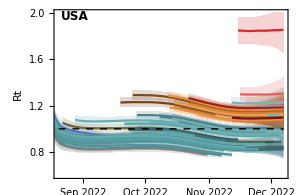
-Graphics- |

```mathematica
fig=Grid[{{countryRtPlot["USA"],legendPanel}},Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-rt.png",fig,"PNG",ImageResolution->300]
```

figures/pango-countries_variant-rt.png

```mathematica
finalRts=Table[If[Length[rtGather["USA",variant]]>0,rtGather["USA",variant][[-1,2]],Null],{variant,variants}];
```

```mathematica
finalRtsLower=Table[If[Length[rtGatherLower["USA",variant]]>0,rtGatherLower["USA",variant][[-1,2]],Null],{variant,variants}];
```

```mathematica
finalRtsUpper=Table[If[Length[rtGatherUpper["USA",variant]]>0,rtGatherUpper["USA",variant][[-1,2]],Null],{variant,variants}];
```

## Prevalence

```mathematica
pData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_I-combined-"<>model<>".tsv"];
```

```mathematica
header=pData[[1]]
```

{date,location,variant,median_I_smooth,I_smooth_upper_95,I_smooth_lower_95,I_smooth_upper_80,I_smooth_lower_80,I_smooth_upper_50,I_smooth_lower_50,median_freq}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_I_smooth→4,I_smooth_upper_95→5,I_smooth_lower_95→6,I_smooth_upper_80→7,I_smooth_lower_80→8,I_smooth_upper_50→9,I_smooth_lower_50→10,median_freq→11}

```mathematica
pData=Drop[pData,1];
```

Only keep data points with incidence

```mathematica
pData=Cases[pData,x_/;x[[4]]>0.9];
```

```mathematica
pGather[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
pGatherLower[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
pGatherUpper[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,7}]]
```

```mathematica
variantCountryPrevalencePlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=pGather[country,variant];
lowerSeries=pGatherLower[country,variant];
upperSeries=pGatherUpper[country,variant];
DateListLogPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated variant cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{200,100000}},DateTicksFormat->{"MonthNameShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{{10,20,100,200,1000,2000,10000,20000,100000,200000,1000000},Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
]
```

```mathematica
countryPrevalencePlot[country_]:=Show[Table[variantCountryPrevalencePlot[country,variants[[i]],colors[[i]]],{i,1,n}]]
```

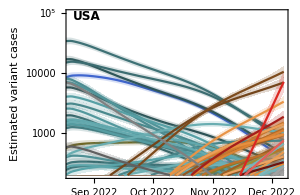
-Graphics- |

```mathematica
fig=Grid[{{countryPrevalencePlot["USA"],legendPanel}},Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-log-cases.png",fig,"PNG",ImageResolution->300]
```

figures/pango-countries_variant-estimated-log-cases.png

```mathematica
variantCountryPrevalencePlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=pGather[country,variant];
lowerSeries=pGatherLower[country,variant];
upperSeries=pGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated variant cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{0,32000}},DateTicksFormat->{"MonthNameShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
]
```

```mathematica
countryPrevalencePlot[country_]:=Show[Table[variantCountryPrevalencePlot[country,variants[[i]],colors[[i]]],{i,1,n}]]
```

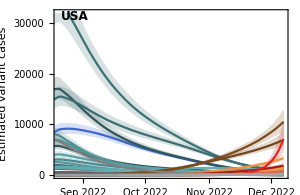
-Graphics- |

```mathematica
fig=Grid[{{countryPrevalencePlot["USA"],legendPanel}},Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-cases.png",fig,"PNG",ImageResolution->300]
```

figures/pango-countries_variant-estimated-cases.png

## Frequency

```mathematica
logitTransform[x_]:=Log[x/(1-x)]
```

```mathematica
logitBackTransform[y_]:=Exp[y]/(1+ Exp[y])
```

```mathematica
logitTicks=Map[{logitTransform[#],ToString[If[#<0.01,NumberForm[Round[100*#,0.1],{3,1}],Round[100*#]]]<>"%"}&,{0.001,0.01,0.1,0.5,0.9,0.99}];
```

```mathematica
fData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_freq-combined-"<>model<>".tsv"];
```

```mathematica
header=fData[[1]]
```

{date,location,variant,median_freq,freq_upper_95,freq_lower_95,freq_upper_80,freq_lower_80,freq_upper_50,freq_lower_50}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_freq→4,freq_upper_95→5,freq_lower_95→6,freq_upper_80→7,freq_lower_80→8,freq_upper_50→9,freq_lower_50→10}

```mathematica
fData=Drop[fData,1];
```

```mathematica
fGather[country_,variant_]:=Cases[fData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
fGatherLower[country_,variant_]:=Cases[fData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
fGatherUpper[country_,variant_]:=Cases[fData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,7}]]
```

```mathematica
logitTransformDateSeries[dateSeries_]:=Map[{#[[1]],Which[#[[2]]<0.0001,logitTransform[0.0001],#[[2]]>0.9999,logitTransform[0.9999],True,logitTransform[#[[2]]]]}&,dateSeries]
```

```mathematica
variantCountryFrequencyPlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=logitTransformDateSeries[fGather[country,variant]];
lowerSeries=logitTransformDateSeries[fGatherLower[country,variant]];
upperSeries=logitTransformDateSeries[fGatherUpper[country,variant]];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated variant frequency"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{logitTransform[0.0005],logitTransform[0.9]}},DateTicksFormat->{"MonthNameShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{logitTicks,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
]
```

```mathematica
countryFrequencyPlot[country_]:=Show[Table[variantCountryFrequencyPlot[country,variants[[i]],colors[[i]]],{i,1,n}]]
```

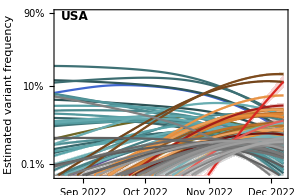
-Graphics- |

```mathematica
fig=Grid[{{countryFrequencyPlot["USA"],legendPanel}},Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-frequency.png",fig,"PNG",ImageResolution->300]
```

figures/pango-countries_variant-estimated-frequency.png

```mathematica
finalFrequencies=Table[fGather["USA",variant][[-1,2]],{variant,variants}];
```

## Rts and frequencies across variants

```mathematica
pos=Flatten[Position[finalRts,x_/;NumberQ[x]]];
```

```mathematica
finalRts=finalRts[[pos]];
```

```mathematica
finalRtsLower=finalRtsLower[[pos]];
```

```mathematica
finalRtsUpper=finalRtsUpper[[pos]];
```

```mathematica
finalFrequencies=finalFrequencies[[pos]];
```

```mathematica
finalVariants=variants[[pos]];
```

```mathematica
finalColors=colors[[pos]];
```

```mathematica
points=ListPlot[Table[{{i,finalRts[[i]]}},{i,Length[finalVariants]}],PlotStyle->finalColors];
```

```mathematica
lines=ListLinePlot[Table[{{i,finalRtsLower[[i]]},{i,finalRtsUpper[[i]]}},{i,Length[finalVariants]}],PlotTheme->"FullAxes",Frame->{True,True,False,False},FrameLabel->{"","Rt"},PlotStyle->Map[Directive[Opacity[0.75],#]&,finalColors],AspectRatio->0.35,ImageSize->600,PlotRange->{rtMin,rtMax},FrameTicks->{{Automatic,Automatic},{Table[{i,Rotate[finalVariants[[i]],Pi/2]},{i,Length[finalVariants]}],Automatic}},Epilog->{Text[Style["USA",Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{0,1},{n,1}}]}];
```

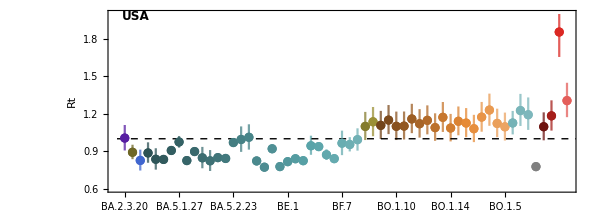

```mathematica
fig=Show[lines,points]
```

```mathematica
Export["figures/"<>dataset<>"_variant-rt-listplot.png",fig,"PNG",ImageResolution->300]
```

figures/pango-countries_variant-rt-listplot.png

```mathematica
topPos=Reverse[Ordering[finalRts,-8]];
```

```mathematica
tableValues=Table[{finalVariants[[p]],Round[finalRts[[p]],0.01],ToString[Round[finalRtsLower[[p]],0.01]]<>" - "<>ToString[Round[finalRtsUpper[[p]],0.01]]},{p,topPos}];
```

```mathematica
table=Style[TableForm[tableValues,TableHeadings->{None,{"lineage","Rt estimate","80% uncertainty interval"}},TableSpacing->{3,1}],FontFamily->"Helvetica",FontSize->12];
```

```mathematica
labels=Table[If[MemberQ[topPos,i],finalVariants[[i]],""],{i,Length[finalRts]}];
```

```mathematica
points=ListPlot[MapThread[{{#1,#2}}&,{finalFrequencies,finalRts}],PlotTheme->"FullAxes",Frame->{True,True,False,False},FrameLabel->{"Current lineage frequency","Rt"},PlotStyle->Map[Directive[Opacity[0.75],#]&,finalColors],AspectRatio->0.65,ImageSize->350,PlotRange->{{0,0.23},{rtMin,rtMax}},FrameTicks->{{Automatic,Automatic},{Table[{i,ToString[Round[100*i]]<>"%"},{i,0,1,0.05}],Automatic}},Epilog->{Text[Style["USA",Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{0,1},{n,1}}]},PlotLabels->Placed[labels,Right]];
```

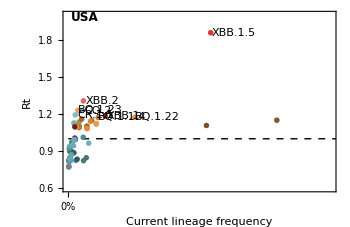
-Graphics- | lineage | Rt estimate | 80% uncertainty interval
XBB.1.5 | 1.86 | 1.66 - 2.07
XBB.2 | 1.31 | 1.17 - 1.45
BQ.1.23 | 1.23 | 1.1 - 1.36
CQ.2 | 1.23 | 1.1 - 1.36
CR.1.1 | 1.19 | 1.07 - 1.33
XBB.1 | 1.18 | 1.07 - 1.31
BQ.1.22 | 1.17 | 1.06 - 1.3
BQ.1.1.4 | 1.17 | 1.05 - 1.29

```mathematica
fig=Grid[{{points,table}}]
```

```mathematica
Export["figures/"<>dataset<>"_variant-rt-top.png",fig,"PNG",ImageResolution->300]
```

figures/pango-countries_variant-rt-top.png